Truss Diagram Analyser

Emilio Vazquez

Jogeva, Gerli /Nachbar, Robert

Harold Washington

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: Create a program that is able to extract information out of truss digram structures and output the physical parameters.

SUMMARY OF WORK: The development of this program can be split into two: the visual processing and the physical quantities calculations. For the first part the development of a reliable image filtering process was necessary in order to extract the graph data structure out of an image. For the second part an algorithm that calculates the n-number of forces of the truss system was implemented.

RESULTS AND FUTURE  WORK: As a future objective for this project is to improve the image processing technique in order to generalize to more complicated truss diagram structures.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

#### Part 1

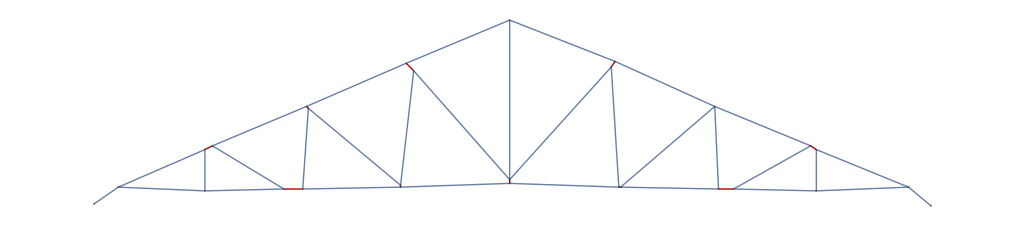

#### Part II

```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

## Tests:

#### a.

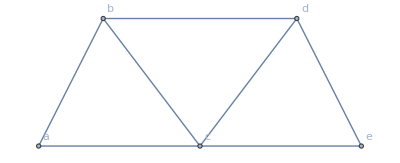

```mathematica
graph=Graph[{a<-> b, b <-> d, d <-> e, a <-> c, c <-> e, c <-> b, c <-> d}, VertexLabels -> Automatic,VertexCoordinates->{{0,0},{2,4},{8,4},{10,0},{5,0}}]
vertexList=graph//VertexList;
vertexCoordinate= PropertyValue[graph,VertexCoordinates];
appliedForces= {{b,{FS1,3*Pi/2}},{c,{FS2,3*Pi/2}},{d,{FS3,3*Pi/2}}};(*Force={Vertex, Force, Angle}*)
supportForces={{a,{S1,Pi/2}},{e,{S2,Pi/2}}};(*Support Forces={Perpendicular to the support base queue,Parallel to the base support queue}*)
parallelSuppor={{a,{Sp,0}}};(*Parallel to the base support queue*)
```

```mathematica
solvingForces[graph,vertexList,vertexCoordinate,appliedForces,supportForces,parallelSuppor]
```

{{F[a b]→0.-0.894427 FS1-0.559017 FS2-0.223607 FS3,F[a c]→0.4 FS1+0.25 FS2+0.1 FS3,F[b d]→-0.25 FS1-0.625 FS2-0.25 FS3,F[b c]→-0.25 FS1+0.625 FS2+0.25 FS3,F[d e]→-0.223607 FS1-0.559017 FS2-0.894427 FS3,F[c d]→0.25 FS1+0.625 FS2-0.25 FS3,F[c e]→0.1 FS1+0.25 FS2+0.4 FS3,S1→0.8 FS1+0.5 FS2+0.2 FS3,S2→0.2 FS1+0.5 FS2+0.8 FS3,Sp→-2.19291×10^-16 FS1+1.8619×10^-16 FS2+1.24127×10^-17 FS3}}

#### b.

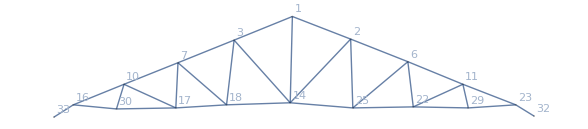

```mathematica
actualGraph
vertexList=actualGraph//VertexList;
vertexCoordinate= PropertyValue[actualGraph,VertexCoordinates];
appliedForces= {{3,{FS1,3*Pi/2}},{1,{FS2,3*Pi/2}},{2,{FS3,3*Pi/2}}};(*Force={Vertex, Force, Angle}*)
supportForces={{16,{S1,Pi/2}},{23,{S2,Pi/2}}};(*Support Forces={Perpendicular to the support base queue,Parallel to the base support queue}*)
parallelSuppor={{16,{Sp,0}}};(*Parallel to the base support queue*)
```

```mathematica
solvingForces[actualGraph,vertexList,vertexCoordinate,appliedForces,supportForces,parallelSuppor]
```

{{F[2]→0.-0.966992 FS1-1.31744 FS2-0.954943 FS3,F[3]→-0.99288 FS1-1.32657 FS2-0.98051 FS3,F[14]→0.754129 FS1+0.0169059 FS2+0.744733 FS3,F[667]→0.764694 FS1+1.04183 FS2+1.31897 FS3,F[736]→0.,F[253]→-0.824027 FS1-1.12267 FS2-1.42131 FS3,F[319]→-0.0688345 FS1-0.0937813 FS2-0.118728 FS3,F[638]→0.777695 FS1+1.05954 FS2+1.34139 FS3,F[480]→1.21736 FS1+0.965491 FS2+0.713624 FS3,F[528]→0.,F[160]→-1.31643 FS1-1.04406 FS2-0.771699 FS3,F[300]→-0.149915 FS1-0.118898 FS2-0.0878814 FS3,F[510]→1.2535 FS1+0.994155 FS2+0.73481 FS3,F[28]→0.0947285 FS1+0.12906 FS2-0.821654 FS3,F[12]→-0.897924 FS1-1.22335 FS2-1.54877 FS3,F[50]→-0.0909378 FS1-0.123895 FS2-0.156852 FS3,F[42]→-0.921476 FS1+0.0337379 FS2+0.0249367 FS3,F[21]→-1.63482 FS1-1.29659 FS2-0.958346 FS3,F[54]→-0.0511343 FS1-0.0405548 FS2-0.0299753 FS3,F[252]→1.51214 FS1+1.19928 FS2+0.886424 FS3,F[350]→0.835114 FS1+1.13777 FS2+1.44043 FS3,F[150]→0.00672834 FS1+0.0091668 FS2+0.0116053 FS3,F[66]→-0.898585 FS1-1.22425 FS2-1.54991 FS3,F[132]→0.00727252 FS1+0.0099082 FS2+0.0125439 FS3,F[126]→0.132787 FS1+0.105313 FS2+0.0778404 FS3,F[70]→-1.51976 FS1-1.20533 FS2-0.890896 FS3,F[119]→-0.138064 FS1-0.109499 FS2-0.0809339 FS3,F[306]→1.41033 FS1+1.11854 FS2+0.826745 FS3,F[550]→0.824401 FS1+1.12318 FS2+1.42195 FS3,F[170]→0.164006 FS1+0.130074 FS2+0.0961414 FS3,F[242]→0.0527032 FS1+0.0718037 FS2+0.0909041 FS3,S1→0.636585 FS1+0.504878 FS2+0.373171 FS3,S2→0.363415 FS1+0.495122 FS2+0.626829 FS3,Sp→8.52651×10^-14 FS1+1.27898×10^-13 FS2+1.42109×10^-13 FS3}}

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

## Tests:

#### a.

```mathematica
graph=Graph[{a<-> b, b <-> d, d <-> e, a <-> c, c <-> e, c <-> b, c <-> d}, VertexLabels -> Automatic,VertexCoordinates->{{0,0},{2,4},{8,4},{10,0},{5,0}}]
vertexList=graph//VertexList;
vertexCoordinate= PropertyValue[graph,VertexCoordinates];
appliedForces= {{b,{FS1,3*Pi/2}},{c,{FS2,3*Pi/2}},{d,{FS3,3*Pi/2}}};(*Force={Vertex, Force, Angle}*)
supportForces={{a,{S1,Pi/2}},{e,{S2,Pi/2}}};(*Support Forces={Perpendicular to the support base queue,Parallel to the base support queue}*)
parallelSuppor={{a,{Sp,0}}};(*Parallel to the base support queue*)
```

-Graphics-

```mathematica
solvingForces[graph,vertexList,vertexCoordinate,appliedForces,supportForces,parallelSuppor]
```

{{F[a b]→0.-0.894427 FS1-0.559017 FS2-0.223607 FS3,F[a c]→0.4 FS1+0.25 FS2+0.1 FS3,F[b d]→-0.25 FS1-0.625 FS2-0.25 FS3,F[b c]→-0.25 FS1+0.625 FS2+0.25 FS3,F[d e]→-0.223607 FS1-0.559017 FS2-0.894427 FS3,F[c d]→0.25 FS1+0.625 FS2-0.25 FS3,F[c e]→0.1 FS1+0.25 FS2+0.4 FS3,S1→0.8 FS1+0.5 FS2+0.2 FS3,S2→0.2 FS1+0.5 FS2+0.8 FS3,Sp→-2.19291×10^-16 FS1+1.8619×10^-16 FS2+1.24127×10^-17 FS3}}

#### b.

```mathematica
actualGraph
vertexList=actualGraph//VertexList;
vertexCoordinate= PropertyValue[actualGraph,VertexCoordinates];
appliedForces= {{3,{FS1,3*Pi/2}},{1,{FS2,3*Pi/2}},{2,{FS3,3*Pi/2}}};(*Force={Vertex, Force, Angle}*)
supportForces={{16,{S1,Pi/2}},{23,{S2,Pi/2}}};(*Support Forces={Perpendicular to the support base queue,Parallel to the base support queue}*)
parallelSuppor={{16,{Sp,0}}};(*Parallel to the base support queue*)
```

-Graphics-

```mathematica
solvingForces[actualGraph,vertexList,vertexCoordinate,appliedForces,supportForces,parallelSuppor]
```

{{F[2]→0.-0.966992 FS1-1.31744 FS2-0.954943 FS3,F[3]→-0.99288 FS1-1.32657 FS2-0.98051 FS3,F[14]→0.754129 FS1+0.0169059 FS2+0.744733 FS3,F[667]→0.764694 FS1+1.04183 FS2+1.31897 FS3,F[736]→0.,F[253]→-0.824027 FS1-1.12267 FS2-1.42131 FS3,F[319]→-0.0688345 FS1-0.0937813 FS2-0.118728 FS3,F[638]→0.777695 FS1+1.05954 FS2+1.34139 FS3,F[480]→1.21736 FS1+0.965491 FS2+0.713624 FS3,F[528]→0.,F[160]→-1.31643 FS1-1.04406 FS2-0.771699 FS3,F[300]→-0.149915 FS1-0.118898 FS2-0.0878814 FS3,F[510]→1.2535 FS1+0.994155 FS2+0.73481 FS3,F[28]→0.0947285 FS1+0.12906 FS2-0.821654 FS3,F[12]→-0.897924 FS1-1.22335 FS2-1.54877 FS3,F[50]→-0.0909378 FS1-0.123895 FS2-0.156852 FS3,F[42]→-0.921476 FS1+0.0337379 FS2+0.0249367 FS3,F[21]→-1.63482 FS1-1.29659 FS2-0.958346 FS3,F[54]→-0.0511343 FS1-0.0405548 FS2-0.0299753 FS3,F[252]→1.51214 FS1+1.19928 FS2+0.886424 FS3,F[350]→0.835114 FS1+1.13777 FS2+1.44043 FS3,F[150]→0.00672834 FS1+0.0091668 FS2+0.0116053 FS3,F[66]→-0.898585 FS1-1.22425 FS2-1.54991 FS3,F[132]→0.00727252 FS1+0.0099082 FS2+0.0125439 FS3,F[126]→0.132787 FS1+0.105313 FS2+0.0778404 FS3,F[70]→-1.51976 FS1-1.20533 FS2-0.890896 FS3,F[119]→-0.138064 FS1-0.109499 FS2-0.0809339 FS3,F[306]→1.41033 FS1+1.11854 FS2+0.826745 FS3,F[550]→0.824401 FS1+1.12318 FS2+1.42195 FS3,F[170]→0.164006 FS1+0.130074 FS2+0.0961414 FS3,F[242]→0.0527032 FS1+0.0718037 FS2+0.0909041 FS3,S1→0.636585 FS1+0.504878 FS2+0.373171 FS3,S2→0.363415 FS1+0.495122 FS2+0.626829 FS3,Sp→8.52651×10^-14 FS1+1.27898×10^-13 FS2+1.42109×10^-13 FS3}}

Code

Provide one of:

Link to the GitHub

Explicit code

Written Content / Lesson Plans

Conclusions in Detail

All Visualizations

#### Part 1

#### Part II

Method of joints

```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

Data Sources Links/References

Future Directions

Background Info Links/References

The analysis algorithm was inspired by the joint method of the analysis of structure presentation from the university of Purdue (Info).

Keywords

Provide keywords as items

Truss

Joint

Filters

Other

Date

5 of July, 2017

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```